```mathematica
GenHeaviside[z_]:=Piecewise[{{HeavisideTheta[Im[z]],Im[z]≠0}},Piecewise[{{0,Re[z]≥0}},1]];
s[a_,b_]:=(-1)^(GenHeaviside[-a]GenHeaviside[-b]GenHeaviside[a b])(-1)^(GenHeaviside[a]GenHeaviside[b]GenHeaviside[-a b]);
```

```mathematica
Clear[x,y1,y2,x0,a]
Fintbabis[x_,y1_,y2_,x0_]:=(2 ArcTan[(√(x-y1) √(x0-y2))/(√(-x0+y1) √(x-y2))])/(√(-x0+y1) √(x0-y2));
Prefactor[a_,y1_,y2_]:=(√-y1 √-y2)/(√(a(-y1) (-y2)));
prefact[a_,y1_,y2_,x_]=(√(x-y1) √(x-y2))/(√(a(x-y1) (x-y2)));
mat[x1_,y1_,x2_,y2_,x3_,y3_]:={{x^2+y^2,x,y,1},{x1^2+y1^2,x1,y1,1},{x2^2+y2^2,x2,y2,1},{x3^2+y3^2,x3,y3,1}};

detmat[x1_,y1_,x2_,y2_,x3_,y3_]:=Det[mat[x1,y1,x2,y2,x3,y3]];

integratetriangle[a_,y1_,y2_,x0_]:=Module[{eqcircle,xsol,xint,abscrit,sign,argcrit,derivcrit,result,prefac,numbranchpoints,tabcrit},

eqcircle=detmat@@Flatten[{ReIm[y1],ReIm[y2],ReIm[x0]}];
xsol=x/.Solve[(eqcircle/.y->0)==0,x];
If[xsol≠{},
xint=Select[xsol,0<#<1&];
(*xint = xsol;*)
abscrit=Abs[(√(x-y1) √(x0-y2))/(√(-x0+y1) √(x-y2))]/.{x->xint};
argcrit=Arg[(√(x-y1) √(x0-y2))/(√(-x0+y1) √(x-y2))]/.{x->xint};
derivcrit=(√(x0-y2))/(√(-x0+y1))D[(√(x-y1))/(√(x-y2)),x]/.{x->xint};
tabcrit={abscrit,argcrit}//Transpose;

numbranchpoints=Count[tabcrit,{abs_,arg_}/;(abs>1&&Abs[arg]==π/2)],
numbranchpoints=0];
(*it gains π when going from positive real plane to negative real plane, and vice-versa*)
sign=If[numbranchpoints==1,If[Re[derivcrit⟦1⟧]<0,1,-1],0];

prefac=Prefactor[a,y1,y2];
result=prefac (√π)/2(sign(2 π)/(√(-x0+y1) √(x0-y2))+(Fintbabis[1,y1,y2,x0])-(Fintbabis[0,y1,y2,x0]));
Print[sign,xint,xsol];
result
]
```

```mathematica
TrianKinem[k21_,k22_,k23_,m1_,m2_,m3_]:=Module[{k1s,k2s,k3s,jac,ks11,ks12,ks22,ks23,ks31,ks33,kinems},
k1s=k21+m1+m2;
k2s=k22+m2+m3;
k3s=k23+m3+m1;
jac=-4 m1 m2 m3 +k1s^2 m3+k2s^2 m1+k3s^2 m2-k1s k2s k3s;

ks11=(-4 m1 m2 + k1s^2)/jac;
ks12=(-2 k3s m2 + k1s k2s)/jac;
ks22=(-4 m2 m3 + k2s^2)/jac;
ks23=(-2 k1s m3 + k2s k3s)/jac;
ks31=(-2 k2s m1 + k1s k3s)/jac;
ks33=(-4 m1 m3 + k3s^2)/jac;

kinems={jac,ks11,ks22,ks33,ks12,ks23,ks31}
];

TrMxy1[y_,k21_,k22_,k23_,m1_,m2_,m3_]:=Module[{Num1,Num0,DeltaR2,DeltaR1,DeltaR0,DeltaS2,DeltaS1,DeltaS0,DiakrS,solS1,solS2,cf1,cf2,DiakrR,solR1,solR2},
Num1=4 k22 y +2 k21-2k22-2k23;
Num0=-4k22 y + 2 m2-2 m3+2 k22;
DeltaR2=-k21 y+k23 y-k23;
DeltaR1=-m2 y+m3 y+k21 y-k23 y+m1-m3+k23;
DeltaR0=m2 y-m3 y+m3;
DeltaS2=-k21^2+2k21 k22+2 k21 k23-k22^2+2 k22 k23-k23^2;DeltaS1=-4*m1*k22-2*m2*k21+2*m2*k22+2*m2*k23+2*m3*k21+2*m3*k22-2*m3*k23-2*k21*k22+2*k22^2-2*k22*k23;DeltaS0=-m2^2+2*m2*m3-2*m2*k22-m3^2-2*m3*k22-k22^2;

DiakrS=√(DeltaS1^2-4 DeltaS2 DeltaS0);

solS1=(-DeltaS1+DiakrS)/(2 DeltaS2);
solS2=(-DeltaS1-DiakrS)/(2 DeltaS2);

cf2=(-(Num1 solS2+Num0))/DiakrS;
cf1=(Num1 solS1+Num0)/DiakrS;

DiakrR=√(DeltaR1^2-4 DeltaR2 DeltaR0);
solR1=(-DeltaR1+DiakrR)/(2 DeltaR2);
solR2=(-DeltaR1-DiakrR)/(2 DeltaR2);

{DeltaR2,solR1,solR2,solS2,solS1,cf2,cf1}
(*cf2 integratetriangle[DeltaR2,solR1,solR2,solS2]+cf1 integratetriangle[DeltaR2,solR1,solR2,solS1]*)
];
TrMxy2[y_,k21_,k22_,k23_,m1_,m2_,m3_]:=Module[{a,y1,y2,x0cf2,x0cf1,cf2,cf1},
{a,y1,y2,x0cf2,x0cf1,cf2,cf1}=TrMxy1[y,k21,k22,k23,m1,m2,m3];
(*Print[integratetriangle[a,y1,y2,x0cf2],integratetriangle[a,y1,y2,x0cf1],y1,y2];*)
cf2 integratetriangle[a,y1,y2,x0cf2]+cf1 integratetriangle[a,y1,y2,x0cf1]
];
TriaMaster[k21_,k22_,k23_,m1_,m2_,m3_]:=TrMxy2[1,k21,k22,k23,m1,m2,m3]-TrMxy2[0,k21,k22,k23,m1,m2,m3];
```

```mathematica
TrNk[n1_,n2_,n3_,k1_,k2_,k3_,M1_,M2_,M3_]:=Module[{k1vec,k2vec,qvec,k1mqvec,k2pqvec,ν2},
k1vec=k1{0,0,1};
ν2=(k3^2-k2^2-k1^2)/(2k1 k2);
k2vec=k2{0,√(1-ν2^2),ν2};
qvec=q{Cos[ϕ]√(1-ν^2),Sin[ϕ]√(1-ν^2),ν};
k1mqvec=k1vec-qvec//Simplify;
k2pqvec=k2vec+qvec//Simplify;
(1/π^(3/2))NIntegrate[q^2/((k1mqvec.k1mqvec+M1)^n1(qvec.qvec+M2)^n2(k2pqvec.k2pqvec+M3)^n3),{q,0,10},{ν,-1,1},{ϕ,0,2π},PrecisionGoal->10,WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
];

TrNkgen[n1_,n2_,n3_,d1_,d2_,d3_,k1_,k2_,k3_,M1_,M2_,M3_]:=Module[{k1vec,k2vec,qvec,k1mqvec,k2pqvec,ν2},
k1vec=k1{0,0,1};
ν2=(1/(2k1 k2))(k3^2-k2^2-k1^2);
k2vec=k2{0,√(1-ν2^2),ν2};
qvec=q{Cos[ϕ]√(1-ν^2),Sin[ϕ]√(1-ν^2),ν};
k1mqvec=k1vec-qvec//Simplify;
k2pqvec=k2vec+qvec//Simplify;
(1/π^(3/2))NIntegrate[q^2 (k1mqvec.k1mqvec)^n1(qvec.qvec)^n2(k2pqvec.k2pqvec)^n3/((k1mqvec.k1mqvec+M1)^d1(qvec.qvec+M2)^d2(k2pqvec.k2pqvec+M3)^d3),{q,0,1000},{ν,-1,1},{ϕ,0,2π},PrecisionGoal->30,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
];
TrN[n1_,n2_,n3_,Q1_,Q2_,Q3_,M1_,M2_,M3_]:=Module[{x1,x2,x3,l1,l2},(Gamma[n1+n2+n3-3/2]/(Gamma[n1]Gamma[n2]Gamma[n3]))NIntegrate[(x1^(n1-1)x2^(n2-1) x3^(n3-1)(1-x1))/(√(x1 x2 Q1+x2 x3 Q2+x3 x1 Q3+ x1 M1 + x2 M2 + x3 M3))^(2n1+2n2+2n3-3)/.{x1->l1,x2->l2(1-l1),x3->(1-l2)(1-l1)},{l1,0,1},{l2,0,1},PrecisionGoal->10,WorkingPrecision->15,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];
```

```mathematica
integratetriangle2[a_,y1_,y2_,x0_]:=Module[{eqcircle,xsol,xint,abscrit,sign,argcrit,derivcrit,result,prefac,numbranchpoints,tabcrit},

eqcircle=detmat@@Flatten[{ReIm[y1],ReIm[y2],ReIm[x0]}];
xsol=x/.Solve[(eqcircle/.y->0)==0,x];
If[xsol≠{},
xint=Select[xsol,#<0&];
(*xint = xsol;*)
abscrit=Abs[(√(x-y1) √(x0-y2))/(√(-x0+y1) √(x-y2))]/.{x->xint};
argcrit=Arg[(√(x-y1) √(x0-y2))/(√(-x0+y1) √(x-y2))]/.{x->xint};
derivcrit=(√(x0-y2))/(√(-x0+y1))D[(√(x-y1))/(√(x-y2)),x]/.{x->xint};
tabcrit={abscrit,argcrit}//Transpose;

numbranchpoints=Count[tabcrit,{abs_,arg_}/;(abs>1&&Abs[arg]==π/2)],
numbranchpoints=0];
(*it gains π when going from positive real plane to negative real plane, and vice-versa*)
sign=If[numbranchpoints==1,If[Re[derivcrit⟦1⟧]<0,1,-1],0];

prefac=Prefactor[a,y1,y2];
result=prefac (√π)/2(sign(2 π)/(√(-x0+y1) √(x0-y2))+(Fintbabis[1,y1,y2,x0])-(Fintbabis[0,y1,y2,x0]));
Print[sign,xsol];
]
integratetriangle3[a_,y1_,y2_,x0_]:=Module[{eqcircle,xsol,xint,abscrit,sign,argcrit,derivcrit,result,prefac,numbranchpoints,tabcrit},

eqcircle=detmat@@Flatten[{ReIm[y1],ReIm[y2],ReIm[x0]}];
xsol=x/.Solve[(eqcircle/.y->0)==0,x];
If[xsol≠{},
xint=Select[xsol,1<#&];
(*xint = xsol;*)
abscrit=Abs[(√(x-y1) √(x0-y2))/(√(-x0+y1) √(x-y2))]/.{x->xint};
argcrit=Arg[(√(x-y1) √(x0-y2))/(√(-x0+y1) √(x-y2))]/.{x->xint};
derivcrit=(√(x0-y2))/(√(-x0+y1))D[(√(x-y1))/(√(x-y2)),x]/.{x->xint};
tabcrit={abscrit,argcrit}//Transpose;

numbranchpoints=Count[tabcrit,{abs_,arg_}/;(abs>1&&Abs[arg]==π/2)],
numbranchpoints=0];
(*it gains π when going from positive real plane to negative real plane, and vice-versa*)
sign=If[numbranchpoints==1,If[Re[derivcrit⟦1⟧]<0,1,-1],0];

prefac=Prefactor[a,y1,y2];
result=prefac (√π)/2(sign(2 π)/(√(-x0+y1) √(x0-y2))+(Fintbabis[1,y1,y2,x0])-(Fintbabis[0,y1,y2,x0]));
Print[sign,xsol];
]
```

```mathematica
(*k1 = 0.5;
k2 = 0.6;
k3 = 0.8;
M1 = -0.1 +0.5 ⅈ;
M2 = -0.2 + 0.4ⅈ;
M3 = 0.2 - 0.3ⅈ;*)
```

```mathematica
(*k1 = 1;
k2 = 1;
k3 =1;
M1 = -0.2 +0.5 ⅈ;
M2 = -0.2+ 0.4ⅈ;
M3 = 0.1- 3.5ⅈ;*)
(*k1 = 1;
k2 = 1;
k3 =1;
M1 = -0.19 +0.5 ⅈ;
M2 = -0.1+ 0.4ⅈ;
M3 = 0.1- 3.ⅈ;*)
(*k1 = 0.3;
k2 = 0.5;
k3 =0.5;
M1 = -0.1 +0.5 ⅈ;
M2 = -0.2+ 0.1ⅈ;
M3 = 0.3- .3ⅈ;*)
(*k1 = 0.3;
k2 = 1;
k3 =1;
M1 = -0.5 +0.4ⅈ;
M2 = -2+ 0.2ⅈ;
M3 =-0.3- 2.ⅈ;*)
(*k1 = 0.3;
k2 = 1;
k3 =1;
M1 = -0.5 +0.4ⅈ;
M2 = -2+ 0.5ⅈ;
M3 =-0.3- 2.ⅈ;*)
(*k1 = 0.1;
k2 = 0.25;
k3 =0.36;
M1 = -0.8 +0.5 ⅈ;
M2 = -0.6+ 0.4ⅈ;
M3 = 0.1- 3.ⅈ;*)
(*k1 = 0.3;
k2 = 0.4;
k3 =0.5;
M1 = -4.1 +0.5 ⅈ;
M2 = -3.2+ 1.6ⅈ;
M3 = 2.3- .3ⅈ;*)
k1 = 0.3;
k2 = 0.4;
k3 =0.5;
M1 = -3.1 +.5 ⅈ;
M3 = -1.2- .6ⅈ;
M2 = 2.3+ 2.6ⅈ;
```

```mathematica
ourres=TriaMaster[k1^2,k2^2,k3^2,M1,M2,M3]
momres=TrNk[1,1,1,k1,k2,k3,M1,M2,M3]
```

0{}{-30.1496,1.42229}

0{0.378527}{-89.6512,0.378527}

0{}{-53.422,-0.807334}

0{}{-4.30469,1.00027}

0.230768+0.402741 ⅈ

-0.0085888625-0.7485312975 ⅈ

```mathematica
NIntegrate[(1-x)/ (M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x))^(3/2),{x,-2000,0},{y,-2000,0}]√π/2
NIntegrate[(1-x)/ (M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x))^(3/2),{x,1,2000},{y,-2000,0}]√π/2
NIntegrate[(1-x)/ (M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x))^(3/2),{x,0,1},{y,1,1000}]√π/2
```

-1.24049-0.58978 ⅈ

1.13354-0.383768 ⅈ

-0.0976329-0.229051 ⅈ

```mathematica
NIntegrate[(1-x)/ (M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x))^(3/2),{x,-2000,0},{y,-2000,0}]√π/2+NIntegrate[(1-x)/ (M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x))^(3/2),{x,1,2000},{y,-2000,0}]√π/2-
NIntegrate[(1-x)/ (M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x))^(3/2),{x,0,1},{y,1,1000}]√π/2
```

-0.00932613-0.744497 ⅈ

```mathematica
k1 = 0.3;
k2 = 0.4;
k3 =0.5;
M1 = -3.1 +.5 ⅈ;
M3 = -1.2- .6ⅈ;
M2 = 2.3+ 2.6ⅈ;
y1=1/(2 (-k2^2+2 k2^2 x-k2^2 x^2))(-k2^2-M2+M3-k1^2 x+2 k2^2 x+k3^2 x+M2 x-M3 x+k1^2 x^2-k2^2 x^2-k3^2 x^2-√(-4 (-k2^2+2 k2^2 x-k2^2 x^2) (M3+k3^2 x+M1 x-M3 x-k3^2 x^2)+(k2^2+M2-M3+k1^2 x-2 k2^2 x-k3^2 x-M2 x+M3 x-k1^2 x^2+k2^2 x^2+k3^2 x^2)^2));
y2=1/(2 (-k2^2+2 k2^2 x-k2^2 x^2))(-k2^2-M2+M3-k1^2 x+2 k2^2 x+k3^2 x+M2 x-M3 x+k1^2 x^2-k2^2 x^2-k3^2 x^2+√(-4 (-k2^2+2 k2^2 x-k2^2 x^2) (M3+k3^2 x+M1 x-M3 x-k3^2 x^2)+(k2^2+M2-M3+k1^2 x-2 k2^2 x-k3^2 x-M2 x+M3 x-k1^2 x^2+k2^2 x^2+k3^2 x^2)^2));
x1=1/(2 (-k3^2-k1^2 y+k2^2 y+k3^2 y-k2^2 y^2))(-k3^2-M1+M3-k1^2 y+2 k2^2 y+k3^2 y+M2 y-M3 y-2 k2^2 y^2-√(-4 (-k3^2-k1^2 y+k2^2 y+k3^2 y-k2^2 y^2) (M3+k2^2 y+M2 y-M3 y-k2^2 y^2)+(k3^2+M1-M3+k1^2 y-2 k2^2 y-k3^2 y-M2 y+M3 y+2 k2^2 y^2)^2));
(*(k3^2+M1-M3-√(4 k3^2 M3+(-k3^2-M1+M3)^2))/(2 k3^2);*)
x2= 1/(2 (-k3^2-k1^2 y+k2^2 y+k3^2 y-k2^2 y^2))(-k3^2-M1+M3-k1^2 y+2 k2^2 y+k3^2 y+M2 y-M3 y-2 k2^2 y^2+√(-4 (-k3^2-k1^2 y+k2^2 y+k3^2 y-k2^2 y^2) (M3+k2^2 y+M2 y-M3 y-k2^2 y^2)+(k3^2+M1-M3+k1^2 y-2 k2^2 y-k3^2 y-M2 y+M3 y+2 k2^2 y^2)^2));
(*(k3^2+M1-M3+√(4 k3^2 M3+(-k3^2-M1+M3)^2))/(2 k3^2);*)
s[y1-1/.x-> 0,1-y2/.x-> 0]
s[y1/.x-> 0,-y2/.x-> 0]
s[x1-1/.y-> 0,1-x2/.y-> 0]
s[x1/.y-> 0,-x2/.y-> 0]
```

1

-1

-1

1

#### Integration in the region x < 0, y < 0

```mathematica
NIntegrate[(1-x)/ (M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x))^(3/2),{x,-1000,0},{y,-1000,0}]√π/2
s[y1/.x-> 0,-y2/.x-> 0](NIntegrate[-(2 (y1+y2))/(k2^3 (-1+x)^2 √y1 (y1-y2)^2 √-y2),{x,-5000,0},PrecisionGoal->10,WorkingPrecision->10]-NIntegrate[(-4 ⅈ)/(k2^3 (-1+x)^2 (y1-y2)^2),{x,-5000,0},PrecisionGoal->10,WorkingPrecision->10])√π/2
(*NIntegrate[(1-x)/((√(k2^2(1-x)^2)√(y1-y)√(y-y2))^3),{x,-100,0},{y,-100,0},PrecisionGoal->15,WorkingPrecision->15]√π/2*)
```

-1.62437-0.558353 ⅈ

-1.62437342-0.55939117 ⅈ

```mathematica
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[0,k1^2,k2^2,k3^2,M1,M2,M3]
cf2 (√π)/2((Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf2]-(2  ArcTan[(√(x0cf2-x1))/(√(-x0cf2+x2))]ⅈ)/(√(k2^2) √(-x0cf2+x2) √(x0cf2-x1))(*-(2 π Prefactor[-k3^2,x1,x2])/(√(x1-x0cf2) √(-x2+x0cf2))*)))+cf1 (√π)/2((Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf1]-(2  ArcTan[(√(x0cf1-x1))/(√(-x0cf1+x2))]ⅈ)/(√(k2^2) √(-x0cf1+x2) √(x0cf1-x1))(*-(2 π Prefactor[-k3^2,x1,x2])/(√(-x0cf1+x2) √(x0cf1-x1))*)))-(Log[-x0cf1]-Log[-x0cf2]-2π ⅈ)/(x0cf1-x0cf2)√π(4  k2 ⅈ)/(2((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3)))
```

{-0.64,0.0113027+0.89379 ⅈ,0.519947+0.35621 ⅈ,0.00729407+0.895097 ⅈ,1.5232-0.611053 ⅈ,0.136749+0.0305071 ⅈ,-4.31386-0.0305071 ⅈ}

12.8261-3.24994 ⅈ

```mathematica
NIntegrate[-(2 (y1+y2))/(k2^3 (-1+x)^2 √y1 (y1-y2)^2 √-y2),{x,-5000,0},PrecisionGoal->10,WorkingPrecision->10]√π/2
cf2 (√π)/2((Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf2]-(2  ArcTan[(√(x0cf2-x1))/(√(-x0cf2+x2))]ⅈ)/(√(k2^2) √(-x0cf2+x2) √(x0cf2-x1))-(2 π Prefactor[-k2^2,x1,x2])/(√(x1-x0cf2) √(-x2+x0cf2))))+cf1 (√π)/2((Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf1]-(2  ArcTan[(√(x0cf1-x1))/(√(-x0cf1+x2))]ⅈ)/(√(k2^2) √(-x0cf1+x2) √(x0cf1-x1))))
```

1.01399497+4.429435434 ⅈ

26.6599+8.12627 ⅈ

```mathematica
NIntegrate[(-4 ⅈ)/(k2^3 (-1+x)^2 (y1-y2)^2),{x,-5000,0},PrecisionGoal->10,WorkingPrecision->10]√π/2
-(Log[-x0cf1]-Log[-x0cf2]-2π ⅈ)/(x0cf1-x0cf2)√π(4  k2 ⅈ)/(2((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3)))
```

2.63836839+4.988826605 ⅈ

2.63837+4.99001 ⅈ

#### Integration in the region x > 1, y < 0

```mathematica
NIntegrate[(1-x)/ (M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x))^(3/2),{x,1,1000},{y,-1000,0}]√π/2
-(NIntegrate[(2 (y1+y2))/(k2^3 (-1+x)^2 √y1 (y1-y2)^2 √-y2),{x,1,1000},PrecisionGoal->10,WorkingPrecision->10]-NIntegrate[(4ⅈ)/(k2^3 (-1+x)^2 (y1-y2)^2),{x,1,100},PrecisionGoal->10,WorkingPrecision->10])√π/2
(*NIntegrate[(1-x)/((√(k2^2(1-x)^2)√(y1-y)√(y-y2))^3),{y,-100,0},{x,1,100},PrecisionGoal->25,WorkingPrecision->25]√π/2*)
```

0.262672-0.295246 ⅈ

-5.1601563+4.09992442 ⅈ

```mathematica
NIntegrate[(2 (y1+y2))/(k2^3 (-1+x)^2 √y1 (y1-y2)^2 √-y2),{x,1,10000},PrecisionGoal->15,WorkingPrecision->15]
NIntegrate[(2 (y1+y2))/(k2^3 (-1+x)^2  (y1-y2)^2 √(-y2 y1)),{x,1,10000},PrecisionGoal->15,WorkingPrecision->15]
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[0,k1^2,k2^2,k3^2,M1,M2,M3];
cf2 (√π)/2(((s[x1-1,1-x2]2  ArcTan[(√(x0cf2-x1))/(√(-x0cf2+x2))]ⅈ)/(√(k2^2) √(-x0cf2+x2) √(x0cf2-x1))-s[x1-1,1-x2]Prefactor[a,x2,x1]Fintbabis[1,x2,x1,x0cf2]))+cf1 (√π)/2(((s[x1-1,1-x2]2  ArcTan[(√(x0cf1-x1))/(√(-x0cf1+x2))]ⅈ)/(√(k2^2) √(-x0cf1+x2) √(x0cf1-x1))-s[x1-1,1-x2]Prefactor[a,x2,x1] Fintbabis[1,x2,x1,x0cf1]))
```

2.2329987760678-4.07533977541396 ⅈ

3.92974832217169-0.75393735025142 ⅈ

3.48265-0.667197 ⅈ

```mathematica
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[0,k1^2,k2^2,k3^2,M1,M2,M3]
NIntegrate[(-2 (y1+y2))/(k2^3 (-1+x)^2  (y1-y2)^2 √(-y2 y1)),{x,1,100},PrecisionGoal->10,WorkingPrecision->10]√π/2
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[0,k1^2,k2^2,k3^2,M1,M2,M3];
cf2 (√π)/2(((s[x1-1,1-x2]2  ArcTan[(√(x0cf2-x1))/(√(-x0cf2+x2))]ⅈ)/(√(k2^2) √(-x0cf2+x2) √(x0cf2-x1))-s[x1-1,1-x2]Prefactor[a,x2,x1]Fintbabis[1,x2,x1,x0cf2]))+cf1 (√π)/2(((s[x1-1,1-x2]2  ArcTan[(√(x0cf1-x1))/(√(-x0cf1+x2))]ⅈ)/(√(k2^2) √(-x0cf1+x2) √(x0cf1-x1))-s[x1-1,1-x2]Prefactor[a,x2,x1] Fintbabis[1,x2,x1,x0cf1]))-(Log[1-x0cf1]-Log[1-x0cf2](*-2π ⅈ*))/(x0cf1-x0cf2)√π(4  k2 ⅈ)/(2((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3)))
```

{-1.,0.00531012+2.51749 ⅈ,0.79469-0.11749 ⅈ,0.96845+2.20545 ⅈ,15.7238-2.06336 ⅈ,0.730169+0.870823 ⅈ,-11.5855-0.870823 ⅈ}

-3.482540431+0.772782401 ⅈ

0.262877-0.295979 ⅈ

```mathematica
Manipulate[{√(-y2 y1),√y1 √-y2},{x,0,0,10}]
```

```mathematica
√y1 √-y2/.x->1.1
√(-y2 y1)/.x->1.1
```

7.57596+10.6331 ⅈ

7.57596+10.6331 ⅈ

```mathematica
NIntegrate[(4ⅈ)/(k2^3 (-1+x)^2 (y1-y2)^2),{x,1,100},PrecisionGoal->10,WorkingPrecision->10]√π/2
-(Log[1-x0cf1]-Log[1-x0cf2](*+2π ⅈ*))/(x0cf1-x0cf2)√π(4  k2 ⅈ)/(2((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3)))
```

-4.90256449-6.829940101 ⅈ

-4.93152-6.88382 ⅈ

```mathematica
integratetriangle3[a,x2,x1,x0cf2]
integratetriangle3[a,x2,x1,x0cf1]
```

0{-0.994972,0.531165}

0{0.875518,33.4127}

#### Integration in the region 0 < x < 1, 1<y

```mathematica
(*NIntegrate[(1-x)/((M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x))^(3/2)),{x,-2000,0},{y,-2000,0}]√π/2+NIntegrate[(1-x)/((M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x))^(3/2)),{x,1,2000},{y,-2000,0}]√π/2-*)NIntegrate[(1-x)/ (M1 x + M2 y(1-x) + M3(1-y)(1-x)+k1^2 x y(1-x) + k2^2(1-x)^2(1-y)y+k3^2 x(1-y)(1-x))^(3/2),{x,0,1},{y,1,1000}]√π/2
s[y1-1/.x-> 0,1-y2/.x-> 0](-NIntegrate[(4-2 (y1+y2))/(k2^3 (-1+x)^2 √(-1+y1) √(1-y2) (y1-y2)^2),{x,0,1},PrecisionGoal->10,WorkingPrecision->10]+NIntegrate[(-4 ⅈ)/(k2^3 (-1+x)^2 (y1-y2)^2),{x,0,1},PrecisionGoal->10,WorkingPrecision->10])√π/2
(*s[y1-1/.x-> 0,1-y2/.x-> 0]NIntegrate[(1-x)/((√(k2^2(1-x)^2)√(y1-y)√(y-y2))^3),{x,0,1},{y,1,100},PrecisionGoal->10,WorkingPrecision->10]√π/2*)
```

-1.36761+0.278991 ⅈ

-1.36861378+0.280163592 ⅈ

```mathematica
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[1,k1^2,k2^2,k3^2,M1,M2,M3];
```

```mathematica
(Log[1-x0cf1]-Log[1-x0cf2]-Log[-x0cf1]+Log[-x0cf2])/(x0cf1-x0cf2)√π(-4   ⅈ k2)/(2((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3)))-cf2 (√π)/2((Prefactor[a,x1,x2] Fintbabis[1,x2,x1,x0cf2]-Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf2]))-cf1 (√π)/2((Prefactor[a,x1,x2] Fintbabis[1,x2,x1,x0cf1]-Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf1](*+(2 π Prefactor[-k3^2,x1,x2])/(√(x1-x0cf1) √(-x2+x0cf1))*)))
```

-1.36861+0.280164 ⅈ

```mathematica
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[0,k1^2,k2^2,k3^2,M1,M2,M3];
cf2 (√π)/2(((-2  ArcTan[(√(x0cf2-x1))/(√(-x0cf2+x2))]ⅈ)/(√(k2^2) √(-x0cf2+x2) √(x0cf2-x1))-Prefactor[-k3^2,x1,x2] Fintbabis[1,x1,x2,x0cf2](*-(2 π Prefactor[-k3^2,x1,x2])/(√(x1-x0cf2) √(-x2+x0cf2))*)))+cf1 (√π)/2(((-2  ArcTan[(√(x0cf1-x1))/(√(-x0cf1+x2))]ⅈ)/(√(k2^2) √(-x0cf1+x2) √(x0cf1-x1))-Prefactor[-k3^2,x1,x2] Fintbabis[1,x1,x2,x0cf1](*-(2 π Prefactor[-k3^2,x1,x2])/(√(-x0cf1+x2) √(x0cf1-x1))*)))
```

13.4295-31.3726 ⅈ

```mathematica
cf2 (√π)/2((Prefactor[-k3^2,x1,x2] Fintbabis[0,x1,x2,x0cf2]+(2  ArcTan[(√(x0cf2-x1))/(√(-x0cf2+x2))]ⅈ)/(√(k2^2) √(-x0cf2+x2) √(x0cf2-x1))(*+(2 π Prefactor[-k3^2,x1,x2])/(√(x1-x0cf2) √(-x2+x0cf2))*)))+cf1 (√π)/2((Prefactor[-k3^2,x1,x2] Fintbabis[0,x1,x2,x0cf1]+(2  ArcTan[(√(x0cf1-x1))/(√(-x0cf1+x2))]ⅈ)/(√(k2^2) √(-x0cf1+x2) √(x0cf1-x1))(*+(2 π Prefactor[-k3^2,x1,x2])/(√(-x0cf1+x2) √(x0cf1-x1))*)))
```

0.0110266+0.365729 ⅈ

```mathematica
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[1,k1^2,k2^2,k3^2,M1,M2,M3]
cf2 (√π)/2((Prefactor[-k2^2,x1,x2] Fintbabis[1,x1,x2,x0cf2]-Prefactor[-k2^2,x1,x2] Fintbabis[0,x1,x2,x0cf2](*+(2 π Prefactor[-k3^2,x1,x2])/(√(x1-x0cf2) √(-x2+x0cf2))*)))+cf1 (√π)/2((Prefactor[-k2^2,x1,x2] Fintbabis[1,x1,x2,x0cf1]-Prefactor[-k2^2,x1,x2] Fintbabis[0,x1,x2,x0cf1](*-(2 π Prefactor[-k3^2,x1,x2])/(√(x1-x0cf1) √(-x2+x0cf1))*)))
```

{-0.0025,-0.971723+2.82071 ⅈ,41.9717-42.8207 ⅈ,2.49971-0.948019 ⅈ,37.5142-40.0955 ⅈ,-0.222685+10.9145 ⅈ,1.61399-10.9145 ⅈ}

4.44079-3.91041 ⅈ

```mathematica
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[0,k1^2,k2^2,k3^2,M1,M2,M3];
cf2 (√π)/2((Prefactor[a,x1,x2] Fintbabis[1,x1,x2,x0cf2]-Prefactor[a,x1,x2] Fintbabis[0,x1,x2,x0cf2](*-(2 π Prefactor[-k3^2,x1,x2])/(√(x1-x0cf2) √(-x2+x0cf2))*)))+cf1 (√π)/2((Prefactor[a,x1,x2] Fintbabis[1,x1,x2,x0cf1]-Prefactor[a,x1,x2] Fintbabis[0,x1,x2,x0cf1](*+(2 π Prefactor[-k3^2,x1,x2])/(√(x1-x0cf1) √(-x2+x0cf1))*)))
```

5.68154-3.05579 ⅈ

```mathematica
TrMxy2[1,k1^2,k2^2,k3^2,M1,M2,M3]
```

{1.62524,3996.}0

{0.491321,192.888}0

6.08778-1.05712 ⅈ

```mathematica
TriaMaster[k1^2,k2^2,k3^2,M1,M2,M3]
```

0{}

0{}

-1{0.548193}

1{0.536741}

0.55634-2.00187 ⅈ

```mathematica
x2/.y-> 1
```

1.30491-0.340178 ⅈ

```mathematica
prefact[a,x2/.y-> 0,x1/.y-> 0,1]
prefact[a,x2/.y-> 0,x1/.y-> 0,0]
```

1.11022×10^-16-1.66667 ⅈ

1.11022×10^-16+1.66667 ⅈ

#### Combining regions

```mathematica
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[0,k1^2,k2^2,k3^2,M1,M2,M3]
reg1=cf2 (√π)/2((Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf2](*-(2  ArcTan[(√(x0cf2-x1))/(√(-x0cf2+x2))]ⅈ)/(√(k2^2) √(-x0cf2+x2) √(x0cf2-x1))*)(*+(2 π Prefactor[a,x1,x2])/(√(x1-x0cf2) √(-x2+x0cf2))*)))+cf1 (√π)/2((Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf1](*-(2  ArcTan[(√(x0cf1-x1))/(√(-x0cf1+x2))]ⅈ)/(√(k2^2) √(-x0cf1+x2) √(x0cf1-x1))*)(*-(2 π Prefactor[-k3^2,x1,x2])/(√(-x0cf1+x2) √(x0cf1-x1))*)))(*-(2π ⅈ)/(x0cf1-x0cf2)√π(4  k2 ⅈ)/(2((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3)))*)
reg2 = cf2 (√π)/2(((*(2  ArcTan[(√(x0cf2-x1))/(√(-x0cf2+x2))]ⅈ)/(√(k2^2) √(-x0cf2+x2) √(x0cf2-x1))*)-s[x1-1,1-x2]Prefactor[a,x2,x1]Fintbabis[1,x2,x1,x0cf2](*+s[x1-1,1-x2](2 π Prefactor[a,x1,x2])/(√(x1-x0cf2) √(-x2+x0cf2))*)))+cf1 (√π)/2(((*(2  ArcTan[(√(x0cf1-x1))/(√(-x0cf1+x2))]ⅈ)/(√(k2^2) √(-x0cf1+x2) √(x0cf1-x1))*)-s[x1-1,1-x2]Prefactor[a,x2,x1] Fintbabis[1,x2,x1,x0cf1]+s[x1-1,1-x2](2 π Prefactor[a,x2,x1])/(√(-x0cf1+x2) √(x0cf1-x1))))+(2π ⅈ)/(x0cf1-x0cf2)√π(4  k2 ⅈ)/(2((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3)))
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[1,k1^2,k2^2,k3^2,M1,M2,M3];
reg3 = (*(Log[1-x0cf1]-Log[1-x0cf2]-Log[-x0cf1]+Log[-x0cf2])/(x0cf1-x0cf2)√π(4   ⅈ k2)/(2((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3)))*)-cf2 (√π)/2((Prefactor[a,x2,x1] Fintbabis[1,x2,x1,x0cf2]-Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf2]))-cf1 (√π)/2((Prefactor[a,x2,x1] Fintbabis[1,x2,x1,x0cf1]-Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf1](*+(2 π Prefactor[a,x2,x1])/(√(x1-x0cf1) √(-x2+x0cf1))*)))
```

{-0.25,-6.31796+5.00322 ⅈ,-0.282045-0.603222 ⅈ,-61.9962-28.4122 ⅈ,2.99621+5.07888 ⅈ,-12.594-0.0771707 ⅈ,1.48289+0.0771707 ⅈ}

-1.80447+0.568305 ⅈ

1.76124-1.5447 ⅈ

-0.0353943-0.227852 ⅈ

```mathematica
reg1+ reg2 -reg3
```

-0.00782706-0.748543 ⅈ

```mathematica
momres
```

-0.0085888625-0.7485312975 ⅈ

```mathematica
Apart[1/((f)(f+M)),f]
```

1/(f M)-1/(M (f+M))

```mathematica
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[1,k1^2,k2^2,k3^2,M1,M2,M3];
integratetriangle[a,x2,x1,x0cf2]
integratetriangle[a,x2,x1,x0cf1]
```

0{}{-30.1496,1.42229}

0.00169068-0.0080863 ⅈ

0{0.378527}{-89.6512,0.378527}

0.0466179+0.0867823 ⅈ

```mathematica
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[0,k1^2,k2^2,k3^2,M1,M2,M3];
integratetriangle2[a,x2,x1,x0cf2]
integratetriangle3[a,x2,x1,x0cf2]
integratetriangle2[a,x2,x1,x0cf1]
integratetriangle3[a,x2,x1,x0cf1]
(*integratetriangle[a,x2,x1,x0cf2]
integratetriangle[a,x2,x1,x0cf1]*)
```

0{-53.422,-0.807334}

0{-53.422,-0.807334}

0{-4.30469,1.00027}

1{-4.30469,1.00027}

```mathematica
x0cf2
x0cf1
```

-61.9962-28.4122 ⅈ

2.99621+5.07888 ⅈ

```mathematica
Manipulate[Arg[x-(3-5.ⅈ)],{x,-100,10,0}]
```

```mathematica
Manipulate[Arg[x-(3-5.ⅈ)],{x,0,0,10}]
```

```mathematica
ComplexPlot[Log[x],{x,3}]
```

-Graphics-

```mathematica
TriaMaster[k1^2,k2^2,k3^2,M1,M2,M3]
```

0{}{1.29346,16.5885}

0{}{1.30865,16.54}

-1{0.965335}{-0.80639,0.965335}

0{0.739693}{0.739693,17.0388}

0.726524-0.535775 ⅈ

```mathematica
TrMxy2[1,k1^2,k2^2,k3^2,M1,M2,M3]
TrMxy2[0,k1^2,k2^2,k3^2,M1,M2,M3]
```

0{}{-0.387903,2.53518}

0{}{-0.851087,1.86581}

6.15289+0.120673 ⅈ

-1{0.531165}{-0.994972,0.531165}

1{0.875518}{0.875518,33.4127}

5.58886+1.92902 ⅈ

```mathematica
{a,x2,x1,x0cf2,x0cf1,cf2,cf1}=TrMxy1[0,k1^2,k2^2,k3^2,M1,M2,M3]
cf2 (√π)/2((-Prefactor[a,x2,x1]Fintbabis[1,x2,x1,x0cf2]+(2 π Prefactor[-k3^2,x1,x2])/(√(x1-x0cf2) √(-x2+x0cf2))))+cf1 (√π)/2((-Prefactor[a,x2,x1] Fintbabis[1,x2,x1,x0cf1](*-(2 π Prefactor[a,x1,x2])/(√(-x0cf1+x2) √(x0cf1-x1))*)))+cf2 (√π)/2((Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf2](*-(2 π Prefactor[a,x1,x2])/(√(x1-x0cf2) √(-x2+x0cf2))*)))+cf1 (√π)/2((Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf1]-(2 π Prefactor[-k3^2,x1,x2])/(√(-x0cf1+x2) √(x0cf1-x1))))
```

{-0.64,0.0113027+0.89379 ⅈ,0.519947+0.35621 ⅈ,0.00729407+0.895097 ⅈ,1.5232-0.611053 ⅈ,0.136749+0.0305071 ⅈ,-4.31386-0.0305071 ⅈ}

-5.58886-1.92902 ⅈ

```mathematica
cf2 (√π)/2((Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf2](*-(2 π Prefactor[a,x1,x2])/(√(x1-x0cf2) √(-x2+x0cf2))*)))+cf1 (√π)/2((Prefactor[a,x2,x1] Fintbabis[0,x2,x1,x0cf1]-(2 π Prefactor[-k3^2,x1,x2])/(√(-x0cf1+x2) √(x0cf1-x1))))
```

-0.349055-6.26035 ⅈ

```mathematica
(2π ⅈ)/(x0cf1-x0cf2)√π(4  k2 ⅈ)/(2((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3)))
(2 π Prefactor[a,x1,x2])/(√(-x0cf1+x2) √(x0cf1-x1))cf1 (√π)/2
```

12.3542+12.2747 ⅈ

-12.3542-12.2747 ⅈ

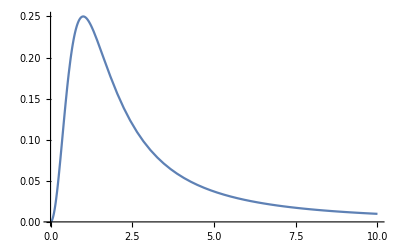

```mathematica
Plot[k^2/((k^2+1)^2),{k,0,10}]
```

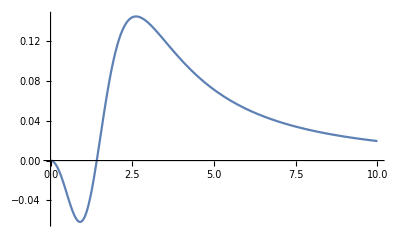

```mathematica
Plot[k^2/((k^2+1-3ⅈ)^2)+k^2/((k^2+1+3ⅈ)^2),{k,0,10}]
```